# 分离变量法求解 非稳态导热微分方程 - 精确解

Piecewise[{{0., x≤0.3}, {-0.3+x, 0.3<x≤0.7}, {-1.11667-3.33333 (-1. x+0.5 x^2), 0.7<x≤1.}, {0.55, True}}]

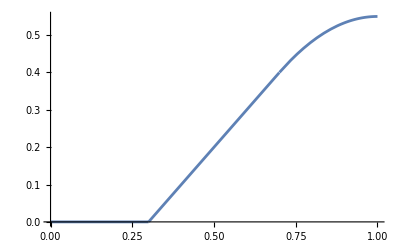

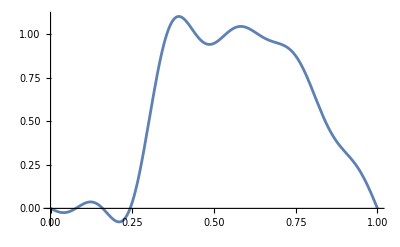

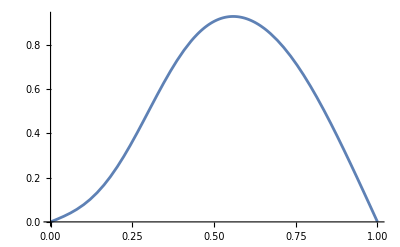

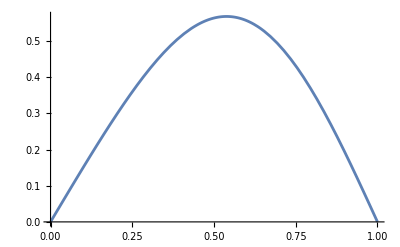

-Graphics3D-

```mathematica
f[x_]:=Piecewise[{{0,0<x<0.3},{1,0.3<=x<=0.7},{-10/3 x+10/3,0.7<=x<=1}}];
g=Integrate[f[x],x]
Plot[g,{x,0,1}]
u=∑_(n=1)^10 ((2∫_0^1 f[x] Sin[n Pi x]ⅆx)Sin[n Pi x] ⅇ^(-n^2 Pi^2 t));
t=0;
Plot[u,{x,0,1}]
t=0.01;
Plot[u,{x,0,1}]
t=0.05;
Plot[u,{x,0,1}]
Plot3D[u,{x,0,1},{t,0,0.01}]
Clear["Global`*"]
```